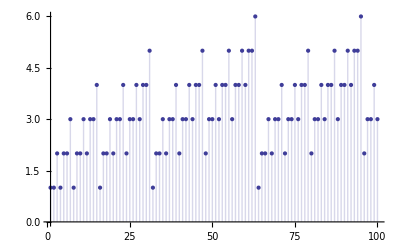

```mathematica
DiscretePlot[Total[IntegerDigits[x,2]],{x,1,100}]
```

```mathematica
∑_(a=0)^100 (1/2^(2a)∑_(i=2^a)^(2^(a+1)-1) Total[IntegerDigits[i,2]])
```

$Aborted

```mathematica
Monitor[Table[∑_(a=0)^n (1/2^(2a)∑_(i=2^a)^(2^(a+1)-1) Total[IntegerDigits[i,2]]),{n,30,30}],{n,a,i}]
```

{3221225455/1073741824}

```mathematica
N[{3221225455/1073741824},100]
```

{2.999999984167516231536865234375}

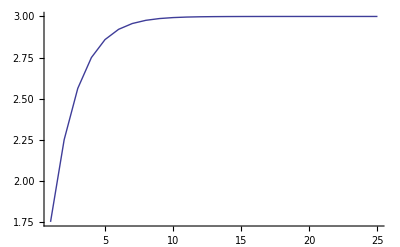

```mathematica
ListPlot[{7/4,9/4,41/16,11/4,183/64,187/64,757/256,381/128,3059/1024,3065/1024,12273/4096,1535/512,49135/16384,49143/16384,196589/65536,98299/32768,786411/262144,786421/262144,3145705/1048576,786429/262144,12582887/4194304,12582899/4194304,50331621/16777216,25165817/8388608,201326563/67108864},Joined->True]
```

```mathematica
N[{7/4,9/4,41/16,11/4,183/64,187/64,757/256,381/128,3059/1024,3065/1024,12273/4096,1535/512,49135/16384,49143/16384,196589/65536,98299/32768,786411/262144,786421/262144,3145705/1048576,786429/262144,12582887/4194304,12582899/4194304,50331621/16777216,25165817/8388608,201326563/67108864},50]//Column
```

1.75
2.25
2.5625
2.75
2.859375
2.921875
2.95703125
2.9765625
2.9873046875
2.9931640625
2.996337890625
2.998046875
2.99896240234375
2.99945068359375
2.9997100830078125
2.999847412109375
2.999919891357421875
2.999958038330078125
2.99997806549072265625
2.999988555908203125
2.9999940395355224609375
2.9999969005584716796875
2.999998390674591064453125
2.99999916553497314453125
2.99999956786632537841796875

```mathematica
∑_(a=0)^∞ (1/2^a c)==3
```

```mathematica
c==3/2
```

```mathematica
3*2^(2a)
```

```mathematica
3/2 2^Floor[Log[x]/Log[2]]+Floor[Log[x]/Log[2]]
```

```mathematica
3*2^(L-1)+L
```

```mathematica
Reduce[3 2^(-1+L)+L==y&&L>0,Integers]
```

(L|y)∈Integers&&L≥1&&y==3 2^(-1+L)+L

Floor::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Floor[Log[4]/Log[2]].

Floor::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Floor[Log[8]/Log[2]].

General::stop: Further output of Floor :: meprec will be suppressed during this calculation.

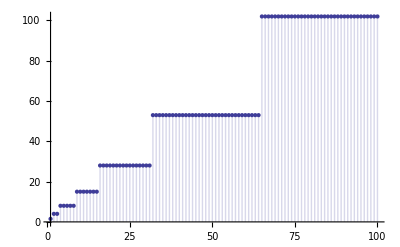

```mathematica
DiscretePlot[3 2^(-1+Floor[Log[x]/Log[2]])+Floor[Log[x]/Log[2]],{x,1,100}]
```

```mathematica
Monitor[Table[∑_(i=1)^(2^a-1) Total[IntegerDigits[i,2]]/(a 2^a),{a,1,20}],{a,i}]
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

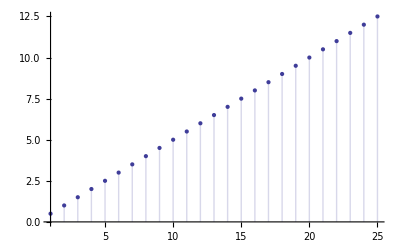

```mathematica
∑_(i=1)^(2^a-1) Total[IntegerDigits[i,2]]==(a 2^a)/2
```

```mathematica
Monitor[Table[∑_(i=1)^a Total[IntegerDigits[i,2]]/(a Log[a]/(Log[2]*2)),{a,2,10000}],{a,i}]
```

{2,(8 Log[2])/(3 Log[3]),(5 Log[2])/(2 Log[4]),(14 Log[2])/(5 Log[5]),(3 Log[2])/Log[6],(24 Log[2])/(7 Log[7]),(13 Log[2])/(4 Log[8]),(10 Log[2])/(3 Log[9]),(17 Log[2])/(5 Log[10]),(40 Log[2])/(11 Log[11]),(11 Log[2])/(3 Log[12]),(50 Log[2])/(13 Log[13]),(4 Log[2])/Log[14],(64 Log[2])/(15 Log[15]),(33 Log[2])/(8 Log[16]),(70 Log[2])/(17 Log[17]),(37 Log[2])/(9 Log[18]),(80 Log[2])/(19 Log[19]),«9964»,(16129 Log[2])/(1248 Log[9984]),(129042 Log[2])/(9985 Log[9985]),(64526 Log[2])/(4993 Log[9986]),(129064 Log[2])/(9987 Log[9987]),(5867 Log[2])/(454 Log[9988]),(129086 Log[2])/(9989 Log[9989]),(64549 Log[2])/(4995 Log[9990]),(129112 Log[2])/(9991 Log[9991]),(64561 Log[2])/(4996 Log[9992]),(129134 Log[2])/(9993 Log[9993]),(64573 Log[2])/(4997 Log[9994]),(25832 Log[2])/(1999 Log[9995]),(32293 Log[2])/(2499 Log[9996]),(129186 Log[2])/(9997 Log[9997]),(64600 Log[2])/(4999 Log[9998]),(43072 Log[2])/(3333 Log[9999]),(64613 Log[2])/(5000 Log[10000])}

```mathematica
N[%]
```

{2.,1.68248,1.25,1.20589,1.16056,1.22128,1.08333,1.05155,1.0235,1.05114,1.02279,1.03938,1.0506,1.09209,1.03125,1.00738,0.985896,0.991195,0.971788,0.97573,0.978519,«9957»,0.972692,0.972735,0.972778,0.972836,0.972788,0.972755,0.972723,0.972705,0.972673,0.972655,0.972637,0.972635,0.972602,0.972585,0.972567,0.972565,0.972547,0.972545,0.972543,0.972555,0.972523}

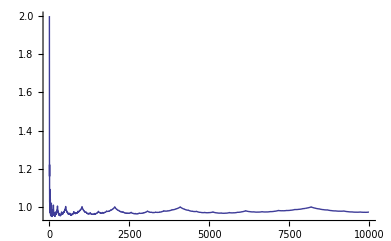

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
Log[a]/(Log[2]*2)+Log[a]/(Log[2])
```

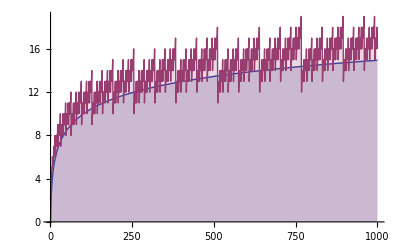

```mathematica
DiscretePlot[{(3 Log[a])/Log[4],Total[IntegerDigits[a,2]]+Length[IntegerDigits[a,2]]},{a,1,1000}]
```

```mathematica
Clear[a,b,c,d]
```

```mathematica
a:=10
c:=5
Reduce[a*x+b==k*a*y+d&&b<a&&d<c,Integers]
```

«1»

```mathematica
a*x+b==c*y+d
a*x-c*y==d-b
```

```mathematica
a:=2
b:=1
c:=3
d:=2
Reduce[d-b==k*GCD[a,c]&&b<a&&d<c&&a>0&&b>0&&c>0&&d>0,Integers]
```

k==1

```mathematica
tf[x_]:=Piecewise[{{0, ToString[x]=="False"}, {1, ToString[x]≠"False"}}]
```

```mathematica
Clear[aa]
aa:=10
```

```mathematica
aa:=100
Monitor[Total[Flatten[Table[{
(Piecewise[{{0, ToString[b<a&&d<c&&a>0&&b>0&&c>0&&d>0]=="False"}, {tf[Reduce[d-b==k*GCD[a,c],Integers]], ToString[b<a&&d<c&&a>0&&b>0&&c>0&&d>0]≠"False"}}])},{a,1,aa},{b,1,aa},{c,1,aa},{d,1,aa}]]],{a,b,c,d}]
```

```mathematica
N[4208627/24010000,100]
```

0.1752864223240316534777176176593086214077467721782590587255310287380258225739275301957517700957934194

```mathematica
2260950/60^4
```

```mathematica
N[15073/86400,100]
```

0.1744560185185185185185185185185185185185185185185185185185185185185185185185185185185185185185185185

```mathematica
1095083/50^4
```

```mathematica
N[1095083/6250000,100]
```

0.17521328

```mathematica
N[108977/640000,100]
```

0.1702765625

```mathematica
135273/30^4
```

```mathematica
N[45091/270000,100]
```

0.1670037037037037037037037037037037037037037037037037037037037037037037037037037037037037037037037037

```mathematica
N[3283/20000,100]$Aborted$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed$Failed
```

0.16415

```mathematica
1415/10000
```

```mathematica
N[283/2000,100]
```

0.1415

```mathematica
2 Mod 3==2,5,(8),11,14 Mod 15
3 Mod 5==3,(8),13 Mod 15
8 Mod 15
```

```mathematica
0==0,3,6,9,12
1==1,4,7,10,13
2==2,5,8,11,14
```

```mathematica
0==0,5,10
1== 1,6,11
2==2,7,12
3==3,8,13
4==4,9,14
```

```mathematica
{0,3}=={{1,2,4},5}
{1,3}=={{0,1,3},5}
{2,3}=={{0,1,4},5}
```

```mathematica
0==0,2,4
1==1,3,5
```

```mathematica
0==0,3
1==1,4
2==2,5
```

```mathematica
{0,2}=={{0,1,2},3}
{1,2}=={{0,1,2},3}
```

```mathematica
a mod b
c mod d
b<a&&d<c
∑_(a=1)^∞ ∑_(b=1)^∞ ∑_(c=1)^∞ ∑_(d=1)^∞ AmodBeqCmodDQ[a,b,c,d]/abcd==???
```

```mathematica
Mod[74-13,36]
```

25

```mathematica
ChineseRemainder[{1,2,5},{2,3,6}]
```

```mathematica
5∈Integers
```

True

```mathematica
ChineseRemainder[{2,3},{3,5}]
```

8

```mathematica
Mod[Subscript[r, i],GCD[Subscript[m, 1],Subscript[m, 2],…]]==Mod[Subscript[r, j],GCD[Subscript[m, 1],Subscript[m, 2],…]]
Mod[1,GCD[2 3,2 5]]==Mod[2,GCD[2 3,2 5]]
```

```mathematica
Reduce[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]]
```

Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]

```mathematica
tf[x_]:=Piecewise[{{0, x==False}, {1, x==True}}]
aa:=50
bb:=Monitor[Table[tf[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]],{a,1,aa},{b,1,aa},{c,1,aa},{d,1,aa}],{a,b,c,d}]
T:=Total[Flatten[bb]]
L:=Length[Flatten[bb]]
T/L
N[T/L]
```

1162521/1562500

0.744013

```mathematica
ToString[ChineseRemainder[{1,2},{2,3}]]
```

5

```mathematica
StringMatchQ[%,NumberString]
```

True

```mathematica
StringMatchQ["ChineseRemainder[{2, 4}, {3, 6}]",NumberString]
```

False

```mathematica
%==False
```

True

```mathematica
StringMatchQ[ToString[ChineseRemainder[{a,c},{b,d}]],NumberString]
```

ChineseRemainder[{a,c},{b,d}]∈Integers

```mathematica
CQ[a_,b_,c_,d_]:=Piecewise[{{0, ToString[a<b&&c<d]=="False"}, {Piecewise[{{0, ToString[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]]=="False"}, {Piecewise[{{0, StringMatchQ[ToString[ChineseRemainder[{a,c},{b,d}]],NumberString]==False}, {1, StringMatchQ[ToString[ChineseRemainder[{a,c},{b,d}]],NumberString]==True}}], ToString[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]]=="True"}}], ToString[a<b&&c<d]=="True"}}]
```

```mathematica
aa:=80
Monitor[Table[CQ[a,b,c,d],{a,1,aa},{b,1,aa},{c,1,aa},{d,1,aa}],{a,b,c,d}]
Flatten[%]
Total[%]/Length[%]
N[%]
```

```mathematica
4208627/24010000
```

0.175286

```mathematica
15073/86400
```

0.174456

```mathematica
1095083/6250000
```

0.175213

```mathematica
1095083/6249999
```

```mathematica
N[%]
```

0.175213

```mathematica
.17
```

```mathematica
.16
```

```mathematica
KQ[a_,b_,c_,d_]:=Piecewise[{{0, ToString[a<b&&c<d]=="False"}, {Piecewise[{{0, ToString[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]]=="False"}, {Piecewise[{{0, StringMatchQ[ToString[ChineseRemainder[{a,c},{b,d}]],NumberString]==False}, {Piecewise[{{0, ChineseRemainder[{a,c},{b,d}]>LCM[b,d]}, {1, ChineseRemainder[{a,c},{b,d}]≤LCM[b,d]}}], StringMatchQ[ToString[ChineseRemainder[{a,c},{b,d}]],NumberString]==True}}], ToString[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]]=="True"}}], ToString[a<b&&c<d]=="True"}}]
```

```mathematica
aa:=90
Monitor[Table[KQ[a,b,c,d],{a,1,aa},{b,1,aa},{c,1,aa},{d,1,aa}],{a,b,c,d}]
Flatten[%]
Total[%]/Length[%]
N[%]
```

$Aborted[]

$Aborted[]

$Aborted

$Aborted

```mathematica
4208627/24010000
```

0.175286

```mathematica
15073/86400
```

0.174456

```mathematica
1095083/6250000
```

0.175213

```mathematica
108977/640000
```

0.170277

```mathematica
45091/270000
```

0.167004

```mathematica
3283/20000
```

0.16415

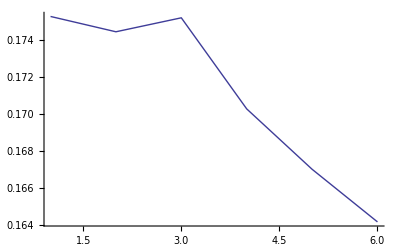

```mathematica
ListPlot[{4208627/24010000,15073/86400,1095083/6250000,108977/640000,45091/270000,3283/20000},Joined->True]
```

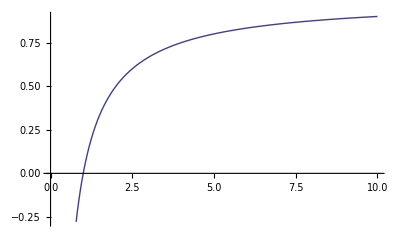

```mathematica
Plot[(x^2-x)/x^2,{x,0,10}]
```

```mathematica
KQ[a_,b_,c_,d_]:=Piecewise[{{0, ToString[a<b&&c<d]=="False"}, {Piecewise[{{0, ToString[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]]=="False"}, {1, ToString[Mod[a,GCD[b,d]]==Mod[c,GCD[b,d]]]=="True"}}], ToString[a<b&&c<d]=="True"}}]
```

```mathematica
QQ[a_,b_,c_,d_]:=Piecewise[{{0, ToString[a<b&&c<d]=="False"}, {1, ToString[a<b&&c<d]=="True"}}]
aa:=100
Monitor[Table[QQ[a,b,c,d],{a,1,aa},{b,1,aa},{c,1,aa},{d,1,aa}],{a,b,c,d}]
Flatten[%]
Total[%]/Length[%]
N[%]
```

```mathematica
9801/40000
```

0.245025

```mathematica
2401/10000
```

0.2401

```mathematica
RandomChoice[{o8,o12,o97,o136,o141,o190,o244,o370,o442,o454,o498,o628,o629,o635,o726,o771,o855,o869,o886,o1084,o1175,o1182,o1186,o1271,o1330,o1522,
a72,a87,a332,a450,a454,a455,a481,a519,a521,a523,a547,a660,a659,a781,a815,a886,a891,a921,a1068,a1076,a1347,a1348,
ag176,ag182,ag218,ag250,ag355,ag463,ag468,ag525,ag750,ag784,ag810,ag941,ag975,ag1072,ag1391,f475,f517,f681,f927,f976,
Ai1,Ai216,Ai270,Ai280,Ai285,Ai311,Ai374,Ai384,Ai391,Ai677,Ai797,Ai848,Aii69,Aii96,Aii268,Aii273,Aii320,Aii387,Aii425,Aii490,Aii475,Aii614,Aii645,Aii659,Aii729,Aii730,Aii780,Aii801,Aii818,Aii932,Aii1045,Aiii18,Aiv91,Aiv96,Aiv120,Aiv221,Aiv239,Aiv411,Aiv545,Aiv622,Av947,Av1140,Avi187,Avi363,Avi402,Avi418,Avi506,Avi595,Avi836,Avii47,Avii422,Aiix987,Aix59,Aix62,Aix252,Aix1030,Aix1054,Aix1100,Ax154,Ax496,Ax845,Axi850,Axi869,Axi903,Axi979,Axi1066,Axii235,Axii444,Axii507,Axii684,Axii900,Axii983,Axii1289}]
```

Aiix987